```mathematica
mat = ConversionMatrix["E","C"];
```

```mathematica
Det[mat]
```

1

```mathematica
vec=With[{base="C"},
Table[Factor[ChromaticPolynomial[allGraphs5[key,"graph"],x]],{key,Bases[base,"AtomKeys"]}]
]
```

{(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-2+x) (-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,x}

```mathematica
mat.vec
```

{x+15 (-1+x) x+25 (-2+x) (-1+x) x+10 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+7 (-1+x) x+6 (-2+x) (-1+x) x+(-3+x) (-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+3 (-1+x) x+(-2+x) (-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x+(-1+x) x,x}

```mathematica
vec.mat
```

{(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+2 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-2+x) (-1+x) x+3 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+4 (-2+x) (-1+x) x+4 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+7 (-2+x) (-1+x) x+6 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+7 (-2+x) (-1+x) x+6 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+7 (-2+x) (-1+x) x+6 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+7 (-2+x) (-1+x) x+6 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,(-1+x) x+7 (-2+x) (-1+x) x+6 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x,x+15 (-1+x) x+25 (-2+x) (-1+x) x+10 (-3+x) (-2+x) (-1+x) x+(-4+x) (-3+x) (-2+x) (-1+x) x}

```mathematica
BasePoly[key_,base_]:=BaseCoeff[key,base]*Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
BasePoly[alfa1Key,"E"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,x^3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-x^2,0,-x^2,0,0,0,0,-x^2,0,0,0,2 x}

```mathematica
Table[allGraphs5[k,"atleast"],{k,Bases["C","AtomKeys"]}]
```

{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,1,1,1}

```mathematica
PolyVect[base_]:=Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
PolyVect["C"]//Simplify
```

{x (24-50 x+35 x^2-10 x^3+x^4),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (-6+11 x-6 x^2+x^3),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),x (2-3 x+x^2),(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,(-1+x) x,x}

```mathematica
PolyMatrix[base1_,base2_]:=Table[BasePoly[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Reverse[PolyVect["E"]].ConversionMatrix["E","C"]//Simplify
```

{x,x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+x),x (1+3 x),x (1+3 x),x (1+3 x),x (1+3 x),x (1+3 x),x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+x)^2,x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+3 x+x^2),x (1+6 x+3 x^2),x (1+6 x+3 x^2),x (1+5 x+4 x^2),x (1+6 x+3 x^2),x (1+4 x+5 x^2),x (1+5 x+3 x^2+x^3),x (1+5 x+3 x^2+x^3),x (1+4 x+4 x^2+x^3),x (1+5 x+3 x^2+x^3),x (1+4 x+4 x^2+x^3),x (1+9 x+4 x^2+x^3),x (1+7 x+6 x^2+x^3),x (1+6 x+7 x^2+x^3),x (1+7 x+6 x^2+x^3),x (1+6 x+7 x^2+x^3),x (1+15 x+25 x^2+10 x^3+x^4)}

```mathematica
Table[Indexed[t,i],{i,1,52}]/.First[Solve[ConversionMatrix["E","C"].Table[Indexed[t,i],{i,1,52}]==PolyVect["E"],Table[Indexed[t,i],{i,1,52}]]]
```

{24 x-50 x^2+35 x^3-10 x^4+x^5,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,2 x-3 x^2+x^3,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,-x+x^2,x}

```mathematica
ConversionMatrix["E","C"].PolyVect["C"]==PolyVect["E"]
```

True

```mathematica
mat2=PolyMatrix["E","C"];MatrixForm[mat2]
```

((-4+x) (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-3+x) (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | x
0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | (-1+x) x | (-1+x) x | x
0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
Det[mat2]
```

(-4+x) (-3+x)^11 (-2+x)^36 (-1+x)^51 x^52

```mathematica
Table[Sum[StirlingS2[5,k],{k,1,m}],{m,1,5}]
```

{1,16,41,51,52}

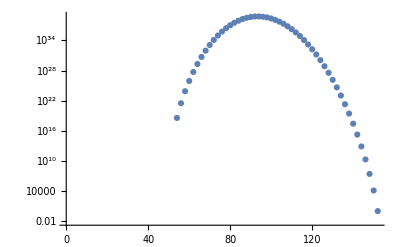

```mathematica
ListLogPlot[CoefficientList[Det[mat2]//Expand,x]]
```

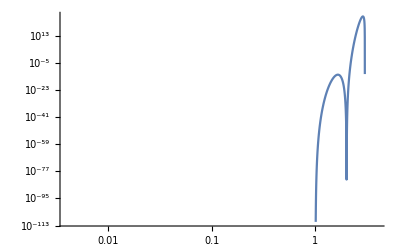

```mathematica
LogLogPlot[Det[mat2],{x,0,4}]
```

```mathematica
Trans[v_]:=Table[{k},{k,v}]
```

```mathematica
VectorQ[BaseCoeff[0,"E"]]
```

True

```mathematica
vec2=BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(BaseCoeff[0,"E"].mat2)//Total//Simplify
```

x^5

```mathematica
PolyMatrix["E","C"]//Det
```

(-4+x) (-3+x)^11 (-2+x)^36 (-1+x)^51 x^52

```mathematica
4!Binomial[x,4]
```

(-3+x) (-2+x) (-1+x) x

```mathematica
empty=Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n12345,n1235x4,n123x45,n124x3x5,n1245x3,n124x35,n125x3x4,n125x34,n12x34x5,n12x345,n12x35x4,n12x3x45,n13x2x4x5,n134x2x5,n1345x2,n134x25,n135x2x4,n135x24,n13x24x5,n13x245,n13x25x4,n13x2x45,n14x2x3x5,n145x2x3,n145x23,n14x23x5,n14x235,n14x25x3,n14x2x35,n15x2x3x4,n15x23x4,n15x234,n15x24x3,n15x2x34,n1x23x4x5,n1x234x5,n1x2345,n1x235x4,n1x23x45,n1x24x3x5,n1x245x3,n1x24x35,n1x25x3x4,n1x25x34,n1x2x34x5,n1x2x345,n1x2x35x4,n1x2x3x45}

```mathematica
Bases["E","Variables"]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
Table[With[{s=k},
If[StringCount[SymbolName[s],"x"]≤2,0,s]],{k,Bases["E","Variables"]}]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
oneEdge=Select[empty,StringCount[SymbolName[#],"x"]==3&]
```

{n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
BaseCoeff[alfa1Key,"E"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,2}

```mathematica
FindRefinements[SymbolToSets[n135x2x4]]
```

{{{1,2,3,5},{4}},{{1,3,4,5},{2}},{{1,3,5},{2,4}}}

```mathematica
rels=Select[
Table[
With[{other=Map[SetsToSymbol[#,"n"]&,FindRefinements[SymbolToSets[v]]]},If[Length[other]≠0,Abs[v]<=Abs[Fold[Plus,other]],{}]],{v,empty}],
!ListQ[#]&];
```

```mathematica
vars=Table[With[{s=k},
If[StringCount[SymbolName[s],"x"]≤2,0,s]],{k,Bases["E","Variables"]}]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vars=Table[k,{k,Bases["E","Variables"]}]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
Table[k==0,{k,Select[Bases["E","Variables"],StringCount[SymbolName[#],"x"]<=3&]}]
```

{n1x2x3x45==0,n1x2x34x5==0,n1x2x35x4==0,n1x23x4x5==0,n1x24x3x5==0,n1x25x3x4==0,n12x3x4x5==0,n13x2x4x5==0,n14x2x3x5==0,n15x2x3x4==0,n1x23x45==0,n1x24x35==0,n1x25x34==0,n12x3x45==0,n12x34x5==0,n12x35x4==0,n13x2x45==0,n13x24x5==0,n13x25x4==0,n14x2x35==0,n14x23x5==0,n14x25x3==0,n15x2x34==0,n15x23x4==0,n15x24x3==0,n1x2x345==0,n1x234x5==0,n1x235x4==0,n1x245x3==0,n123x4x5==0,n124x3x5==0,n125x3x4==0,n134x2x5==0,n135x2x4==0,n145x2x3==0,n12x345==0,n123x45==0,n124x35==0,n125x34==0,n13x245==0,n134x25==0,n135x24==0,n14x235==0,n145x23==0,n15x234==0,n1x2345==0,n1234x5==0,n1235x4==0,n1245x3==0,n1345x2==0,n12345==0}

```mathematica
Table[k->Factor[Total[(vars.mat2/.x->k)]],{k,1,5}]//TableForm
```

1→n12345+n1234x5+n1235x4+n123x45+n123x4x5+n1245x3+n124x35+n124x3x5+n125x34+n125x3x4+n12x345+n12x34x5+n12x35x4+n12x3x45+n12x3x4x5+n1345x2+n134x25+n134x2x5+n135x24+n135x2x4+n13x245+n13x24x5+n13x25x4+n13x2x45+n13x2x4x5+n145x23+n145x2x3+n14x235+n14x23x5+n14x25x3+n14x2x35+n14x2x3x5+n15x234+n15x23x4+n15x24x3+n15x2x34+n15x2x3x4+n1x2345+n1x234x5+n1x235x4+n1x23x45+n1x23x4x5+n1x245x3+n1x24x35+n1x24x3x5+n1x25x34+n1x25x3x4+n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45+n1x2x3x4x5
2→2 (n12345+2 n1234x5+2 n1235x4+2 n123x45+4 n123x4x5+2 n1245x3+2 n124x35+4 n124x3x5+2 n125x34+4 n125x3x4+2 n12x345+4 n12x34x5+4 n12x35x4+4 n12x3x45+8 n12x3x4x5+2 n1345x2+2 n134x25+4 n134x2x5+2 n135x24+4 n135x2x4+2 n13x245+4 n13x24x5+4 n13x25x4+4 n13x2x45+8 n13x2x4x5+2 n145x23+4 n145x2x3+2 n14x235+4 n14x23x5+4 n14x25x3+4 n14x2x35+8 n14x2x3x5+2 n15x234+4 n15x23x4+4 n15x24x3+4 n15x2x34+8 n15x2x3x4+2 n1x2345+4 n1x234x5+4 n1x235x4+4 n1x23x45+8 n1x23x4x5+4 n1x245x3+4 n1x24x35+8 n1x24x3x5+4 n1x25x34+8 n1x25x3x4+4 n1x2x345+8 n1x2x34x5+8 n1x2x35x4+8 n1x2x3x45+16 n1x2x3x4x5)
3→3 (n12345+3 n1234x5+3 n1235x4+3 n123x45+9 n123x4x5+3 n1245x3+3 n124x35+9 n124x3x5+3 n125x34+9 n125x3x4+3 n12x345+9 n12x34x5+9 n12x35x4+9 n12x3x45+27 n12x3x4x5+3 n1345x2+3 n134x25+9 n134x2x5+3 n135x24+9 n135x2x4+3 n13x245+9 n13x24x5+9 n13x25x4+9 n13x2x45+27 n13x2x4x5+3 n145x23+9 n145x2x3+3 n14x235+9 n14x23x5+9 n14x25x3+9 n14x2x35+27 n14x2x3x5+3 n15x234+9 n15x23x4+9 n15x24x3+9 n15x2x34+27 n15x2x3x4+3 n1x2345+9 n1x234x5+9 n1x235x4+9 n1x23x45+27 n1x23x4x5+9 n1x245x3+9 n1x24x35+27 n1x24x3x5+9 n1x25x34+27 n1x25x3x4+9 n1x2x345+27 n1x2x34x5+27 n1x2x35x4+27 n1x2x3x45+81 n1x2x3x4x5)
4→4 (n12345+4 n1234x5+4 n1235x4+4 n123x45+16 n123x4x5+4 n1245x3+4 n124x35+16 n124x3x5+4 n125x34+16 n125x3x4+4 n12x345+16 n12x34x5+16 n12x35x4+16 n12x3x45+64 n12x3x4x5+4 n1345x2+4 n134x25+16 n134x2x5+4 n135x24+16 n135x2x4+4 n13x245+16 n13x24x5+16 n13x25x4+16 n13x2x45+64 n13x2x4x5+4 n145x23+16 n145x2x3+4 n14x235+16 n14x23x5+16 n14x25x3+16 n14x2x35+64 n14x2x3x5+4 n15x234+16 n15x23x4+16 n15x24x3+16 n15x2x34+64 n15x2x3x4+4 n1x2345+16 n1x234x5+16 n1x235x4+16 n1x23x45+64 n1x23x4x5+16 n1x245x3+16 n1x24x35+64 n1x24x3x5+16 n1x25x34+64 n1x25x3x4+16 n1x2x345+64 n1x2x34x5+64 n1x2x35x4+64 n1x2x3x45+256 n1x2x3x4x5)
5→5 (n12345+5 n1234x5+5 n1235x4+5 n123x45+25 n123x4x5+5 n1245x3+5 n124x35+25 n124x3x5+5 n125x34+25 n125x3x4+5 n12x345+25 n12x34x5+25 n12x35x4+25 n12x3x45+125 n12x3x4x5+5 n1345x2+5 n134x25+25 n134x2x5+5 n135x24+25 n135x2x4+5 n13x245+25 n13x24x5+25 n13x25x4+25 n13x2x45+125 n13x2x4x5+5 n145x23+25 n145x2x3+5 n14x235+25 n14x23x5+25 n14x25x3+25 n14x2x35+125 n14x2x3x5+5 n15x234+25 n15x23x4+25 n15x24x3+25 n15x2x34+125 n15x2x3x4+5 n1x2345+25 n1x234x5+25 n1x235x4+25 n1x23x45+125 n1x23x4x5+25 n1x245x3+25 n1x24x35+125 n1x24x3x5+25 n1x25x34+125 n1x25x3x4+25 n1x2x345+125 n1x2x34x5+125 n1x2x35x4+125 n1x2x3x45+625 n1x2x3x4x5)

```mathematica
(5/2)^4
```

625/16

```mathematica
3^4
```

81

```mathematica
4^4
```

256

```mathematica
(vars.mat2/.x->2)//Total
```

16 n12x3x4x5+16 n13x2x4x5+16 n14x2x3x5+16 n15x2x3x4+16 n1x23x4x5+16 n1x24x3x5+16 n1x25x3x4+16 n1x2x34x5+16 n1x2x35x4+16 n1x2x3x45+32 n1x2x3x4x5

```mathematica
Solve[((vars.mat2//Total)/.x->4)==0,x]
```

{}

```mathematica
mat3=PolyMatrix["C","E"];MatrixForm[mat3]
```

((-4+x) (-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | -(-3+x) (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | 2 (-2+x) (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -2 (-1+x) x | -6 (-1+x) x | -6 (-1+x) x | -6 (-1+x) x | -6 (-1+x) x | -6 (-1+x) x | 24 x
0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | (-1+x) x | 2 (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | 2 (-1+x) x | 0 | 0 | 2 (-1+x) x | 2 (-1+x) x | -6 x
0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 2 (-1+x) x | 0 | (-1+x) x | 0 | 0 | 0 | (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | 0 | 0 | 2 (-1+x) x | -6 x
0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | (-1+x) x | 0 | 2 (-1+x) x | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 0 | 0 | 2 (-1+x) x | 0 | 2 (-1+x) x | 0 | 2 (-1+x) x | -6 x
0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 2 (-1+x) x | (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | 0 | 0 | -6 x
0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 0 | 2 (-1+x) x | 0 | 0 | (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | 0 | 2 (-1+x) x | 0 | -6 x
0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | (-1+x) x | 2 (-1+x) x | 0 | (-1+x) x | 0 | 0 | 2 (-1+x) x | 0 | 2 (-1+x) x | 2 (-1+x) x | 0 | -6 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 2 (-1+x) x | (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | 0 | -6 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | 2 (-1+x) x | (-1+x) x | (-1+x) x | 0 | 0 | 0 | 0 | 2 (-1+x) x | 2 (-1+x) x | 0 | 2 (-1+x) x | -6 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | 2 (-1+x) x | (-1+x) x | 0 | 0 | 2 (-1+x) x | 0 | 2 (-1+x) x | 2 (-1+x) x | -6 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3+x) (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+x) (-1+x) x | 0 | -(-2+x) (-1+x) x | -(-2+x) (-1+x) x | 0 | 0 | 0 | (-1+x) x | 0 | 0 | (-1+x) x | 0 | (-1+x) x | 2 (-1+x) x | 0 | 0 | 2 (-1+x) x | 2 (-1+x) x | 2 (-1+x) x | -6 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | -(-1+x) x | 0 | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 0 | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+x) (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1+x) x | 0 | 0 | 0 | 0 | -(-1+x) x | -(-1+x) x | 2 x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | 0 | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1+x) x | -x
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
MatrixRank[mat3]
```

52

```mathematica
(mat3)/.x->1//MatrixRank
```

1

```mathematica
Table[v->Coefficient[allGraphs5[0,"colofourrealnull"],v],{v,Bases["E","Variables"]}]
```

{n1x2x3x4x5→1,n1x2x3x45→0,n1x2x34x5→0,n1x2x35x4→0,n1x23x4x5→0,n1x24x3x5→0,n1x25x3x4→0,n12x3x4x5→0,n13x2x4x5→0,n14x2x3x5→0,n15x2x3x4→0,n1x23x45→0,n1x24x35→0,n1x25x34→0,n12x3x45→0,n12x34x5→0,n12x35x4→0,n13x2x45→0,n13x24x5→0,n13x25x4→0,n14x2x35→0,n14x23x5→0,n14x25x3→0,n15x2x34→0,n15x23x4→0,n15x24x3→0,n1x2x345→0,n1x234x5→0,n1x235x4→0,n1x245x3→0,n123x4x5→0,n124x3x5→0,n125x3x4→0,n134x2x5→0,n135x2x4→0,n145x2x3→0,n12x345→0,n123x45→0,n124x35→0,n125x34→0,n13x245→0,n134x25→0,n135x24→0,n14x235→0,n145x23→0,n15x234→0,n1x2345→0,n1234x5→0,n1235x4→0,n1245x3→0,n1345x2→0,n12345→0}

```mathematica
rels[[1]]
```

n1x2x3x4x5==-n12x3x4x5-n13x2x4x5-n14x2x3x5-n15x2x3x4-n1x23x4x5-n1x24x3x5-n1x25x3x4-n1x2x34x5-n1x2x35x4-n1x2x3x45

```mathematica
Table[v->Style[ToString[Coefficient[allGraphs5[K5Key,"colofourrealnull"],v]],Red],{v,Bases["E","Variables"]}]
```

{n1x2x3x4x5→1,n1x2x3x45→-1,n1x2x34x5→-1,n1x2x35x4→-1,n1x23x4x5→-1,n1x24x3x5→-1,n1x25x3x4→-1,n12x3x4x5→-1,n13x2x4x5→-1,n14x2x3x5→-1,n15x2x3x4→-1,n1x23x45→1,n1x24x35→1,n1x25x34→1,n12x3x45→1,n12x34x5→1,n12x35x4→1,n13x2x45→1,n13x24x5→1,n13x25x4→1,n14x2x35→1,n14x23x5→1,n14x25x3→1,n15x2x34→1,n15x23x4→1,n15x24x3→1,n1x2x345→2,n1x234x5→2,n1x235x4→2,n1x245x3→2,n123x4x5→2,n124x3x5→2,n125x3x4→2,n134x2x5→2,n135x2x4→2,n145x2x3→2,n12x345→-2,n123x45→-2,n124x35→-2,n125x34→-2,n13x245→-2,n134x25→-2,n135x24→-2,n14x235→-2,n145x23→-2,n15x234→-2,n1x2345→-6,n1234x5→-6,n1235x4→-6,n1245x3→-6,n1345x2→-6,n12345→24}

```mathematica
n1x2x3x4x5+
```

```mathematica
rels[[1]]/.Table[v->Style[ToString[Coefficient[allGraphs5[K5Key,"colofourrealnull"],v]],Red],{v,Bases["E","Variables"]}]
```

1==-10 -1

```mathematica
rels/.Table[v->Style[ToString[Coefficient[allGraphs5[K5Key,"colofourrealnull"],v]],Red],{v,Bases["E","Variables"]}]//ExpressionToTable
```

SymbolName::sym: Argument 1 at position 1 is expected to be a symbol.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[1],1].

SymbolName::sym: Argument 2 at position 1 is expected to be a symbol.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[2],1].

SymbolName::sym: Argument 1 at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[1],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[1],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[1],1],3,0] is not a list of digits or a string of valid digits.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[2],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[2],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[2],1],3,0] is not a list of digits or a string of valid digits.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[2],1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[2],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[2],1],3,0].

General::stop: Further output of StringPadLeft::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[2],1],3,0] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

1==-10 -1
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
-2+24==0
24+-6==0
24+-6==0
24+-6==0
24+-6==0
24+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
1+2 -2+-6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-2+2+2 -6==0
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)
-1==-3 (1+2)

```mathematica
rels/.Table[v->Coefficient[allGraphs5[0,"colofourrealnull"],v],{v,Bases["E","Variables"]}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}